### Correction Factor θmeas = ArcTan[Cos[θ -ωT],Sin[θ]] θ-θmeas = θ-ArcTan[Cos[θ -ωT],Sin[θ]]

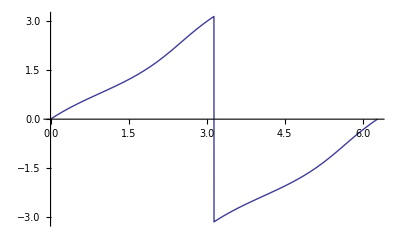

```mathematica
Plot[ArcTan[Cos[θ-ωT],Sin[θ]],{θ,0,2π}]
```

```mathematica
TrigReduce[FullSimplify[θ-ArcTan[Cos[θ-ωT],Sin[θ]],triginverses=all]]
```

θ-ArcTan[Cos[θ-ωT],Sin[θ]]

```mathematica
FullSimplify[Solve[{θmeas==ArcTan[Cos[θ-ωT],Sin[θ]]},θ]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{θ→-ⅈ Log[-(ⅈ ⅇ^((ⅈ ωT)/2) √(1+ⅇ^(2 ⅈ θmeas)+ⅇ^(ⅈ ωT) (-1+ⅇ^(2 ⅈ θmeas))))/(√(-1+ⅇ^(2 ⅈ θmeas)-2 Cos[θmeas] (Cos[θmeas+ωT]+ⅈ Sin[θmeas+ωT])))]},{θ→-ⅈ Log[(ⅈ ⅇ^((ⅈ ωT)/2) √(1+ⅇ^(2 ⅈ θmeas)+ⅇ^(ⅈ ωT) (-1+ⅇ^(2 ⅈ θmeas))))/(√(-1+ⅇ^(2 ⅈ θmeas)-2 Cos[θmeas] (Cos[θmeas+ωT]+ⅈ Sin[θmeas+ωT])))]},{θ→-ⅈ Log[-(√(ⅇ^(ⅈ ωT)-ⅇ^(2 ⅈ ωT)))/(√(1+ⅇ^(ⅈ ωT)))]},{θ→1/2 ⅈ (Log[1+ⅇ^(ⅈ ωT)]-Log[ⅇ^(ⅈ ωT)-ⅇ^(2 ⅈ ωT)])}}

```mathematica
Clear[ωT,θmeas]
Solve[{θmeas==ArcTan[Cos[θ-ωT],Sin[θ]]&&θ>0&&θ<π/2&&ωT>0 &&ωT<π/200},θ]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{θmeas==ArcTan[Cos[θ-ωT],Sin[θ]]&&θ>0&&θ<π/2&&ωT>0&&ωT<π/200},θ]

```mathematica
Clear[ωT]
θm=ArcTan[Cos[θ-ωT],Sin[θ]]; 
ExpToTrig[FullSimplify[Series[θ-θm,{ωT,0,2}]]]
```

(θ+ⅈ Log[ⅇ^(ⅈ θ)])+Sin[θ]^2 ωT+(-1/2 Sin[2 θ]+1/8 Sin[4 θ]) ωT^2+O[ωT]^3

```mathematica
Clear[ωT]
θm=ArcTan[Cos[θ-ωT],Sin[θ]]; 
FourierCosSeries[θ-θm/.ωT->1 2π 1/100,θ,1]
```

$Aborted

```mathematica
θ-θm/.ωT->1 2π 1/100
```

θ-ArcTan[Cos[π/50-θ],Sin[θ]]

```mathematica
Clear[err,θmeas]
```

```mathematica
N[25 π/180 100/(2π)]
```

6.94444

```mathematica
FullSimplify[ωT/2(1- Cos[2 θmeas[θ]])]
```

ωT Sin[θmeas[θ]]^2

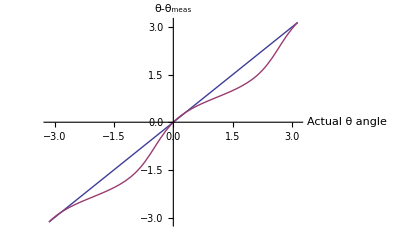

```mathematica
ωT =1 2π 1/10;
θmeas[θ_]:=ArcTan[Cos[θ-ωT],Sin[θ]]; 
err[θ_] := θ-θmeas[θ];
Plot[{θ,θmeas[θ]},{θ,-π,π},AxesOrigin->{0,0}, AxesLabel-> {"Actual θ angle","θ-θ_meas"} ]
```

```mathematica
ArcTan[Cos[θ-ωT],Sin[θ]]/.{ωT -> 2π 1/100}
```

ArcTan[Cos[π/50-θ],Sin[θ]]

```mathematica
FourierCosSeries[θ-ArcTan[Cos[π/50-θ],Sin[θ]],θ,2]
```

```mathematica
1/π∫_-π^π (θ-ArcTan[Cos[π/50-θ],Sin[θ]])Cos[n θ]ⅆθ
```

$Aborted

### What is the penalty for loss of resolution given a measurement Mx?

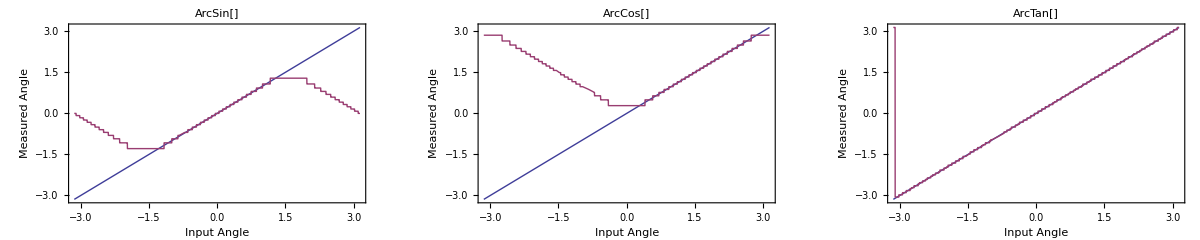

```mathematica
ac =Plot[{θ,ArcCos[Round[ Cos[θ],2/25]]},{θ,-π,π},Frame->{True,True,False,False},FrameLabel-> {"Input Angle","Measured Angle"},PlotLabel->"ArcCos[]"];
as =Plot[{θ,ArcSin[Round[Sin[θ],2/25]]},{θ,-π,π},Frame->{True,True,False,False},FrameLabel-> {"Input Angle","Measured Angle"},PlotLabel->"ArcSin[]"];
at=Plot[{θ,ArcTan[Round[ Cos[θ],2/25],Round[Sin[θ],2/25]]},{θ,-π,π},Frame->{True,True,False,False},FrameLabel-> {"Input Angle","Measured Angle"},PlotLabel->"ArcTan[]"];
GraphicsRow[{as,ac,at},ImageSize->{1000}]
```

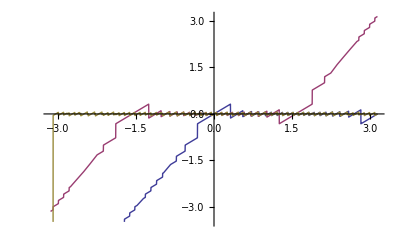

```mathematica
Res = 20;
Plot[{
θ-ArcCos[Round[ Cos[θ],2/Res]],
θ-ArcSin[Round[ Sin[θ],2/Res]],
θ-ArcTan[Round[ Cos[θ],2/Res],Round[Sin[θ],2/Res]]
},{θ,-π,π},FrameLabel-> {"Input Angle","Measured Angle"}]
```

### Is there a simpler formula? Yes! ωΔT/2(1- Cos[2 θ]) == ωΔT Sin[θ]^2, but this obscures that we used Fourier series to find the coefficients.

```mathematica
θmeas[θ_]:=ArcTan[Cos[θ-ωT],Sin[θ]];
SimCorrect[θ_]:=θmeas[θ]+ωT/2(1- Cos[2 θmeas[θ]]);
```

```mathematica
FullSimplify[SimCorrect[θ]]
```

ArcTan[Cos[θ-ωT],Sin[θ]]+ωT Sin[ArcTan[Cos[θ-ωT],Sin[θ]]]^2

```mathematica
FullSimplify[ωT/2(1- Cos[2 θ])]
```

ωT Sin[θ]^2

### Numerically Integrate Fourier Cosine Series

```mathematica
(* Here I integrate over Subscript[θ, M1]   Approximately the 2^nd-order Fourier cosine series -- just remember the first coefficient is 1/2 a0   *)
Hz=10;
cosCoeff = Chop[Table[Quiet[NIntegrate[1/π(θ-ArcTan[Cos[θ-Hz π/50],Sin[θ]])Cos[n ArcTan[Cos[θ-Hz π/50],Sin[θ]]],{θ,-π,π}]],{n,0,6}]];
sinCoeff =Chop[Table[Quiet[NIntegrate[1/π(θ-ArcTan[Cos[θ-Hz π/50],Sin[θ]])Sin[n ArcTan[Cos[θ-Hz π/50],Sin[θ]]],{θ,-π,π}]],{n,0,6}]];
ωΔT = Hz π/50;
StringForm["ωΔT = ``",N[ωΔT]]
StringForm["1/ωΔTCosine coefficients are = ``",cosCoeff/ωΔT]
StringForm["1/ωΔTSine coefficients are = ``",sinCoeff/ωΔT]
```

ωΔT = 0.628319

1/ωΔTCosine coefficients are = {1., 0, -0.488814, 0, -0.105573, 0, 0.095573}

1/ωΔTSine coefficients are = {0, 0, 0.32492, 0, -0.239714, 0, -0.0343027}

```mathematica
(* approximately the 2^nd-order Fourier cosine series -- just remember the first coefficient is 1/2 a0*)
Hz=10;
cosCoeff = Chop[Table[Quiet[NIntegrate[1/π(θ-ArcTan[Cos[θ-Hz π/50],Sin[θ]])Cos[n θ],{θ,-π,π}]],{n,0,6}]];
sinCoeff =Chop[Table[Quiet[NIntegrate[1/π(θ-ArcTan[Cos[θ-Hz π/50],Sin[θ]])Sin[n θ],{θ,-π,π}]],{n,0,6}]];
ωΔT = Hz π/50;
StringForm["ωΔT = ``",N[ωΔT]]
StringForm["1/ωΔTCosine coefficients are = ``",cosCoeff/ωΔT]
StringForm["1/ωΔTSine coefficients are = ``",sinCoeff/ωΔT]
```

ωΔT = 0.628319

1/ωΔTCosine coefficients are = {1., 0, -0.418364, 0, -0.0799003, 0, -0.00562353}

1/ωΔTSine coefficients are = {0, 0, -0.303959, 0, 0.0259612, 0, 0.0173075}

```mathematica
FourierCosCoefficient[θ-ArcTan[Cos[π/50-θ],Sin[θ]],θ,0]
```

$Aborted

```mathematica
FourierCosCoefficient[θ-ArcTan[Cos[π/50-θ],Sin[θ]],θ,1]
```

1/π 2 (-2-1/(4 √(-(-1+(-1)^(1/25))^2))(-1)^(3/100) (2 (-1+(-1)^(24/25)) (√(1-(-1)^(1/25)) ArcTan[((-1)^(1/100) (-2+(-1)^(1/50)+(-1)^(49/50)))/(2 √(-1+(-1)^(1/25)))]-√(-1+(-1)^(1/25)) ArcTan[((-1)^(1/100) (2+(-1)^(1/50)+(-1)^(49/50)))/(2 √(1-(-1)^(1/25)))])+(-1)^(23/50) (1+(-1)^(1/25)) (√(-1+(-1)^(1/25)) (Log[-((-1)^(3/100) (-1+(-1)^(24/25)))/(√(1-(-1)^(1/25)))]-Log[((-1)^(3/100) (-1+(-1)^(24/25)))/(√(1-(-1)^(1/25)))])+√(1-(-1)^(1/25)) (-Log[-((-1)^(3/100) (-1+(-1)^(24/25)))/(√(-1+(-1)^(1/25)))]+Log[((-1)^(3/100) (-1+(-1)^(24/25)))/(√(-1+(-1)^(1/25)))]))))

-0.00150824-9.01157×10^-16 ⅈ

0.0015708

```mathematica
FourierCosCoefficient[θ-ArcTan[Cos[π/50-θ],Sin[θ]],θ,2]
```

1/(4 (-1+(-1)^(1/25)) π)(2 (-1)^(12/25) (1+(-1)^(1/25))^2 π+(-2-2 (-1)^(1/25)+(-1)^(3/50)+(-1)^(49/50)) Log[(ⅈ+(-1)^(27/50))/(1+2 (-1)^(1/50)-(-1)^(1/25))]+2 Log[(ⅈ+(-1)^(27/50))/(-1-2 (-1)^(1/50)+(-1)^(1/25))]+2 (-1)^(1/25) Log[(ⅈ+(-1)^(27/50))/(-1-2 (-1)^(1/50)+(-1)^(1/25))]-(-1)^(3/50) Log[(ⅈ+(-1)^(27/50))/(-1-2 (-1)^(1/50)+(-1)^(1/25))]-(-1)^(49/50) Log[(ⅈ+(-1)^(27/50))/(-1-2 (-1)^(1/50)+(-1)^(1/25))]+2 Log[-(ⅈ+(-1)^(27/50))/(-1+2 (-1)^(1/50)+(-1)^(1/25))]+2 (-1)^(1/25) Log[-(ⅈ+(-1)^(27/50))/(-1+2 (-1)^(1/50)+(-1)^(1/25))]+(-1)^(3/50) Log[-(ⅈ+(-1)^(27/50))/(-1+2 (-1)^(1/50)+(-1)^(1/25))]+(-1)^(49/50) Log[-(ⅈ+(-1)^(27/50))/(-1+2 (-1)^(1/50)+(-1)^(1/25))]-2 Log[(ⅈ+(-1)^(27/50))/(-1+2 (-1)^(1/50)+(-1)^(1/25))]-2 (-1)^(1/25) Log[(ⅈ+(-1)^(27/50))/(-1+2 (-1)^(1/50)+(-1)^(1/25))]-(-1)^(3/50) Log[(ⅈ+(-1)^(27/50))/(-1+2 (-1)^(1/50)+(-1)^(1/25))]-(-1)^(49/50) Log[(ⅈ+(-1)^(27/50))/(-1+2 (-1)^(1/50)+(-1)^(1/25))])

```mathematica
N[1/(4 (-1+(-1)^(1/25)) π)(2 (-1)^(12/25) (1+(-1)^(1/25))^2 π+(-2-2 (-1)^(1/25)+(-1)^(3/50)+(-1)^(49/50)) Log[(ⅈ+(-1)^(27/50))/(1+2 (-1)^(1/50)-(-1)^(1/25))]+2 Log[(ⅈ+(-1)^(27/50))/(-1-2 (-1)^(1/50)+(-1)^(1/25))]+2 (-1)^(1/25) Log[(ⅈ+(-1)^(27/50))/(-1-2 (-1)^(1/50)+(-1)^(1/25))]-(-1)^(3/50) Log[(ⅈ+(-1)^(27/50))/(-1-2 (-1)^(1/50)+(-1)^(1/25))]-(-1)^(49/50) Log[(ⅈ+(-1)^(27/50))/(-1-2 (-1)^(1/50)+(-1)^(1/25))]+2 Log[-(ⅈ+(-1)^(27/50))/(-1+2 (-1)^(1/50)+(-1)^(1/25))]+2 (-1)^(1/25) Log[-(ⅈ+(-1)^(27/50))/(-1+2 (-1)^(1/50)+(-1)^(1/25))]+(-1)^(3/50) Log[-(ⅈ+(-1)^(27/50))/(-1+2 (-1)^(1/50)+(-1)^(1/25))]+(-1)^(49/50) Log[-(ⅈ+(-1)^(27/50))/(-1+2 (-1)^(1/50)+(-1)^(1/25))]-2 Log[(ⅈ+(-1)^(27/50))/(-1+2 (-1)^(1/50)+(-1)^(1/25))]-2 (-1)^(1/25) Log[(ⅈ+(-1)^(27/50))/(-1+2 (-1)^(1/50)+(-1)^(1/25))]-(-1)^(3/50) Log[(ⅈ+(-1)^(27/50))/(-1+2 (-1)^(1/50)+(-1)^(1/25))]-(-1)^(49/50) Log[(ⅈ+(-1)^(27/50))/(-1+2 (-1)^(1/50)+(-1)^(1/25))])]
N[- 2π 1/100/2]
```

-0.0313643-1.60982×10^-15 ⅈ

-0.0314159

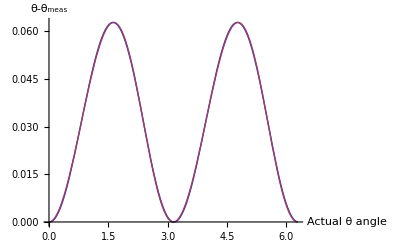

```mathematica
ωT =1 2π 1/100;
θmeas[θ_]:=ArcTan[Cos[θ-ωT],Sin[θ]]; 
err[θ_] := θ-θmeas[θ];
Plot[{If[err[θ]>π,err[θ]-2π,err[θ]],ωT/2(1- Cos[2 θmeas[θ]])},{θ,0,2π},AxesOrigin->{0,0}, AxesLabel-> {"Actual θ angle","θ-θ_meas"} ]
```

```mathematica
Manipulate[Plot[{θmeas[θ],θmeas[θ]+ωT/2(1- Cos[2 θmeas[θ]])},{θ,-π,π},AxesOrigin->{0,0}, AxesLabel-> {"Actual θ angle","θ-θ_meas"},PlotLabel->"θ_meas (15) and corrected θ_meas (16)"],{ωT,-5,25}]
```

```mathematica
N[2π 10]
```

62.8319

```mathematica
Clear[ωT]
Manipulate[Module[{θ,θmeas,err,Corrected1,Corrected2,Corrected3,Corrected4,ωT,SimCorrect},
ωT = Hz 2 π/100;
θmeas[θ_]:=ArcTan[Cos[θ-ωT],Sin[θ]];
err[θ_] := θ-θmeas[θ];
SimCorrect[θ_]:=θmeas[θ]+ωT/2(1- Cos[2 θmeas[θ]]);

Plot[{θ,
If[θmeas[θ]<0,θmeas[θ]+2π,θmeas[θ]],

If[SimCorrect[θ]<0,SimCorrect[θ]+2π,SimCorrect[θ]]

},{θ,0,2π},AxesOrigin->{0,0},FrameLabel-> {"Rotor angle [rad]","Reconstructed
 measurements [rad]"},(*PlotLabel->"θ, θ_M1, and corrected θ_M",*)
Frame->{{True,True},{True,True}},
FrameTicks->{{0,Pi/2,Pi,3Pi/2,2Pi,3Pi},{0,Pi/2,Pi,3Pi/2,2Pi,3Pi},None,None},PlotRange->{{0,2π},{0,2π}},
ImageSize->Large,AspectRatio->1/3, PlotStyle->{Automatic,Directive[Thick,Dashed],Directive[Thick,Dashing[{0.025,0.01}]]},FrameTicksStyle->Directive[22],BaseStyle->{FontSize->18}
]],{{Hz,10,"Hz"},-15,15,Appearance->"Labeled"}]
```

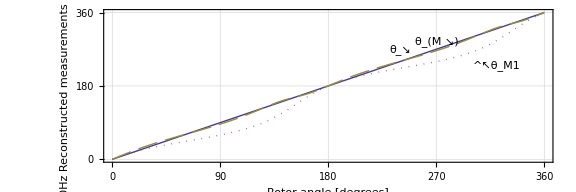

```mathematica
Clear[ωT]
Hz = 10;
Module[{θ,θrad,θmeas,err,Corrected1,Corrected2,Corrected3,Corrected4,ωT,SimCorrect},
ωT = Hz 2 π/100;
θmeas[θ_]:=ArcTan[Cos[θ-ωT],Sin[θ]];
err[θ_] := θ-θmeas[θ];
SimCorrect[θ_]:=θmeas[θ]+ωT/2(1- Cos[2 θmeas[θ]]);
θ = θrad π/180;
Plot[{180/π θ,
180/π If[θmeas[θ]<0,θmeas[θ]+2π,θmeas[θ]],

180/π If[SimCorrect[θ]<0,SimCorrect[θ]+2π,SimCorrect[θ]]

},{θrad,0,360},AxesOrigin->{0,0},FrameLabel-> {"Rotor angle [degrees]","θ̇ = 10Hz Reconstructed
 measurements [degrees]"},(*PlotLabel->"θ, θ_M1, and corrected θ_M",*)
Frame->{{True,True},{True,True}},
FrameTicks->{{0,90,180,270,360},{0,90,180,270,360},None,None},PlotRange->{{0,360},{0,360}},
ImageSize->Large,AspectRatio->1/3, PlotStyle->{Automatic,Directive[Thick,Dotted],Directive[Thick,Dashing[{0.025,0.01}]]},FrameTicksStyle->Directive[22],BaseStyle->{FontSize->18},GridLines->Automatic,GridLinesStyle->Directive[Dotted,Lighter[Gray]],
Epilog->{Text["^↖θ_M1",{320,230}],Text["θ_(M ↘)",{270,290}],Text["θ_↘",{240,270}]}
]]
```

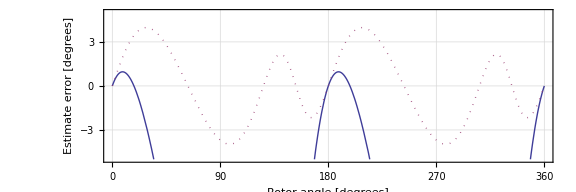

```mathematica
Clear[ωT]
Hz = 10;
Module[{θ,θrad,θmeas,err,Corrected1,Corrected2,Corrected3,Corrected4,ωT,SimCorrect},
ωT = Hz 2 π/100;
θmeas[θ_]:=ArcTan[Cos[θ-ωT],Sin[θ]];
err[θ_] := θ-θmeas[θ];
SimCorrect[θ_]:=θmeas[θ]+ωT/2(1- Cos[2 θmeas[θ]]);
θ = θrad π/180;
Plot[{
180/π( If[θmeas[θ]<0,θmeas[θ]+2π,θmeas[θ]]-θ),

180/π( If[SimCorrect[θ]<0,SimCorrect[θ]+2π,SimCorrect[θ]]-θ)

},{θrad,0,360},AxesOrigin->{0,0},FrameLabel-> {"Rotor angle [degrees]","
 Estimate error [degrees]"},(*PlotLabel->"θ, θ_M1, and corrected θ_M",*)
Frame->{{True,True},{True,True}},
FrameTicks->{{0,90,180,270,360},Automatic,None,None},PlotRange->{{0,360},{-5,5}},
ImageSize->Large,AspectRatio->1/3, PlotStyle->{Automatic,Directive[Thick,Dotted],Directive[Thick,Dashing[{0.025,0.01}]]},FrameTicksStyle->Directive[22],BaseStyle->{FontSize->18},GridLines->Automatic,GridLinesStyle->Directive[Dotted,Lighter[Gray]],
Epilog->{Text["^↖θ_M1",{320,230}],Text["θ_(M ↘)",{270,290}],Text["θ_↘",{240,270}]}
]]
```

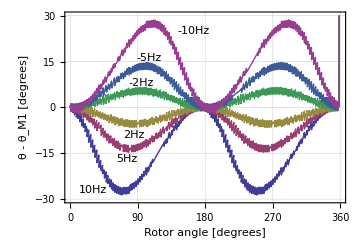

```mathematica
Module[{θ,θrad,θmeas,err,Corrected1,Corrected2,Corrected3,Corrected4,ωT,SimCorrect,Hzs,Res},
Res = 50;
splitstyle[styles__]:=Module[{st=Directive/@{styles}},{{Last[st=RotateLeft@st],#}}&];
θmeas[θ_]:=ArcTan[Round[Cos[θ-ωT],2/Res],Round[Sin[θ],2/Res]];
err[θ_] := θ-θmeas[θ];
Hzs={-10,-5,-2,2,5,10};
SimCorrect[θ_]:=θmeas[θ]+ωT/2(1- Cos[2 θmeas[θ]]);
Plot[
{Evaluate[Table[
ωT = Hz 2 π*0.0075;
θ = θrad π/180;
180/π( θ-If[θmeas[θ]<0,θmeas[θ]+2π,θmeas[θ]])
,{Hz,Hzs}]]}
,{θrad,0,360},AxesOrigin->{0,0},FrameLabel-> {"Rotor angle [degrees]","θ - θ_M1 [degrees]"},(*PlotLabel->"θ, θ_M1, and corrected θ_M",*)
Frame->{{True,True},{True,True}},PlotStyle->{Thick,splitstyle@@ColorData[1]/@{1,2,3,4,5,6}},
FrameTicks->{{0,90,180,270,360},Automatic,None,None},PlotRange->{{0,360},{-30,30}},
ImageSize->Medium,AspectRatio->2/3, FrameTicksStyle->Directive[22],BaseStyle->{FontSize->18},GridLines->Automatic,GridLinesStyle->Directive[Dotted,Lighter[Gray]],
Epilog->{Text["-10Hz",{165,25}],Text["-5Hz",{105,16}],Text["-2Hz",{95,8}],Text["2Hz",{85,-9}],Text["5Hz",{75,-17}],Text["10Hz",{30,-27}]}
]]
```

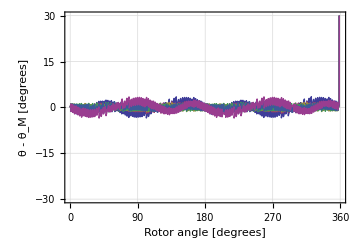

```mathematica
Module[{θ,θrad,θmeas,err,Corrected1,Corrected2,Corrected3,Corrected4,ωT,SimCorrect,Hzs,Res},
Res = 50;
splitstyle[styles__]:=Module[{st=Directive/@{styles}},{{Last[st=RotateLeft@st],#}}&];
θmeas[θ_]:=ArcTan[Round[Cos[θ-ωT],2/Res],Round[Sin[θ],2/Res]];
err[θ_] := θ-θmeas[θ];
Hzs={-10,-5,-2,2,5,10};
SimCorrect[θ_]:=θmeas[θ]+ωT/2(1- Cos[2 θmeas[θ]]);
Plot[
{Evaluate[Table[
ωT = Hz 2 π*0.0075;
θ = θrad π/180;
180/π( θ-If[SimCorrect[θ]<0,SimCorrect[θ]+2π,SimCorrect[θ]])
,{Hz,Hzs}]]}
,{θrad,0,360},AxesOrigin->{0,0},FrameLabel-> {"Rotor angle [degrees]","θ - θ_M [degrees]"},(*PlotLabel->"θ, θ_M1, and corrected θ_M",*)
Frame->{{True,True},{True,True}},PlotStyle->{Thick,splitstyle@@ColorData[1]/@{1,2,3,4,5,6}},
FrameTicks->{{0,90,180,270,360},Automatic,None,None},PlotRange->{{0,360},{-30,30}},
ImageSize->Medium,AspectRatio->2/3, FrameTicksStyle->Directive[22],BaseStyle->{FontSize->18},GridLines->Automatic,GridLinesStyle->Directive[Dotted,Lighter[Gray]]  (*less than 2 degrees error!*)
]]
```

### ParametricPLotting!

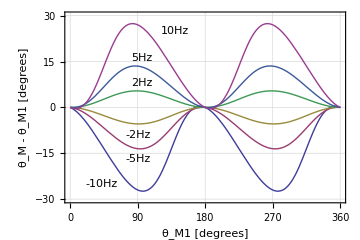

```mathematica
Module[{θ,θrad,θmeas,err,Corrected1,Corrected2,Corrected3,Corrected4,ωT,SimCorrect,Hzs,θM1},
splitstyle[styles__]:=Module[{st=Directive/@{styles}},{{Last[st=RotateLeft@st],#}}&];
θmeas[θ_]:=ArcTan[Cos[θ-ωT],Sin[θ]];
err[θ_] := θ-θmeas[θ];
Hzs={-10,-5,-2,2,5,10};
SimCorrect[θ_]:=θmeas[θ]+ωT/2(1- Cos[2 θmeas[θ]]);
ParametricPlot[
{Evaluate[Table[
ωT = Hz 2 π*0.0075;
θ = θrad π/180;
θM1 =If[θmeas[θ]<0,θmeas[θ]+2π,θmeas[θ]];
{180/π θM1,180/π( θ-θM1)}
,{Hz,Hzs}]]}
,{θrad,0,360},AxesOrigin->{0,0},FrameLabel-> {"θ_M1 [degrees]","θ_M - θ_M1 [degrees]"},(*PlotLabel->"θ, θ_M1, and corrected θ_M",*)
Frame->{{True,True},{True,True}},PlotStyle->{Thick,splitstyle@@ColorData[1]/@{1,2,3,4,5,6}},
FrameTicks->{{0,90,180,270,360},Automatic,None,None},PlotRange->{{0,360},{-30,30}},
ImageSize->Medium,AspectRatio->2/3, FrameTicksStyle->Directive[22],BaseStyle->{FontSize->18},GridLines->Automatic,GridLinesStyle->Directive[Dotted,Lighter[Gray]],
Epilog->{Text["10Hz",{140,25}],Text["5Hz",{95,16}],Text["2Hz",{95,8}],Text["-2Hz",{90,-9}],Text["-5Hz",{90,-17}],Text["-10Hz",{42,-25}]}
]]
```

```mathematica
Module[{θ,θrad,θmeas,err,Corrected1,Corrected2,Corrected3,Corrected4,ωT,SimCorrect,Hzs,θM1},
θmeas[θ_]:=ArcTan[Cos[θ-ωT],Sin[θ]];
err[θ_] := θ-θmeas[θ];
SimCorrect[θ_]:=θmeas[θ]+ωT/2(1- Cos[2 θmeas[θ]]);
Hzs = .1;
{Maximize[
ωT =Hzs 2 π*0.0075;
θ = θrad π/180;
θM1 =If[θmeas[θ]<0,θmeas[θ]+2π,θmeas[θ]];
{180/π( θ-θM1),θrad≥0, θrad≤ 360}
,{θrad}],
Maximize[
ωT =Hzs 2 π*0.0075;
θ = θrad π/180;
θM1 =If[θmeas[θ]<0,θmeas[θ]+2π,θmeas[θ]];
{180/π( θ-If[SimCorrect[θ]<0,SimCorrect[θ]+2π,SimCorrect[θ]]),θrad≥0, θrad≤ 360}
,{θrad}]}
]
```

{{0.27,{θrad$177966→270.203}},{0.000158691,{θrad$177966→337.556}}}

```mathematica
27.391188832117738/2.031588847597971  (*10*)
5.4030028955633185/0.0665585660916344(*2*)
2.7003748926525817/0.01626463784559519(*1*)
0.27000037472810134/0.00015869050835874238(*.10*)
```

13.4826

81.1767

166.027

1701.43

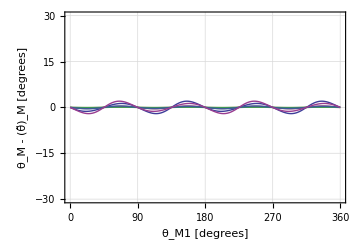

```mathematica
Module[{θ,θrad,θmeas,err,Corrected1,Corrected2,Corrected3,Corrected4,ωT,SimCorrect,Hzs,θM1,θtilde },
splitstyle[styles__]:=Module[{st=Directive/@{styles}},{{Last[st=RotateLeft@st],#}}&];
θmeas[θ_]:=ArcTan[Cos[θ-ωT],Sin[θ]];
err[θ_] := θ-θmeas[θ];
Hzs={-10,-5,-2,2,5,10};
SimCorrect[θ_]:=θmeas[θ]+ωT/2(1- Cos[2 θmeas[θ]]);
ParametricPlot[
{Evaluate[Table[
ωT = Hz 2 π*0.0075;
θ = θrad π/180;
θM1 =If[θmeas[θ]<0,θmeas[θ]+2π,θmeas[θ]];
{180/π θM1,180/π( θ-If[SimCorrect[θ]<0,SimCorrect[θ]+2π,SimCorrect[θ]])}

,{Hz,Hzs}]]}
,{θrad,0,360},AxesOrigin->{0,0},FrameLabel-> {"θ_M1 [degrees]","θ_M - (θ̃)_M [degrees]"},(*PlotLabel->"θ, θ_M1, and corrected θ_M",*)
Frame->{{True,True},{True,True}},PlotStyle->{Thick,splitstyle@@ColorData[1]/@{1,2,3,4,5,6}},
FrameTicks->{{0,90,180,270,360},Automatic,None,None},PlotRange->{{0,360},{-30,30}},
ImageSize->Medium,AspectRatio->2/3, FrameTicksStyle->Directive[22],BaseStyle->{FontSize->18},GridLines->Automatic,GridLinesStyle->Directive[Dotted,Lighter[Gray]]  (*less than 2 degrees error!*)
]]
```

## As a function of θ

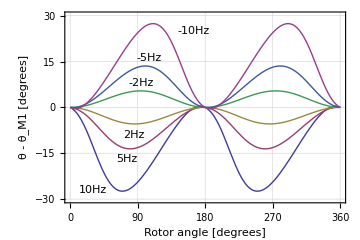

```mathematica
Module[{θ,θrad,θmeas,err,Corrected1,Corrected2,Corrected3,Corrected4,ωT,SimCorrect,Hzs},
splitstyle[styles__]:=Module[{st=Directive/@{styles}},{{Last[st=RotateLeft@st],#}}&];
θmeas[θ_]:=ArcTan[Cos[θ-ωT],Sin[θ]];
err[θ_] := θ-θmeas[θ];
Hzs={-10,-5,-2,2,5,10};
SimCorrect[θ_]:=θmeas[θ]+ωT/2(1- Cos[2 θmeas[θ]]);
Plot[
{Evaluate[Table[
ωT = Hz 2 π*0.0075;
θ = θrad π/180;
180/π( θ-If[θmeas[θ]<0,θmeas[θ]+2π,θmeas[θ]])
,{Hz,Hzs}]]}
,{θrad,0,360},AxesOrigin->{0,0},FrameLabel-> {"Rotor angle [degrees]","θ - θ_M1 [degrees]"},(*PlotLabel->"θ, θ_M1, and corrected θ_M",*)
Frame->{{True,True},{True,True}},PlotStyle->{Thick,splitstyle@@ColorData[1]/@{1,2,3,4,5,6}},
FrameTicks->{{0,90,180,270,360},Automatic,None,None},PlotRange->{{0,360},{-30,30}},
ImageSize->Medium,AspectRatio->2/3, FrameTicksStyle->Directive[22],BaseStyle->{FontSize->18},GridLines->Automatic,GridLinesStyle->Directive[Dotted,Lighter[Gray]],
Epilog->{Text["-10Hz",{165,25}],Text["-5Hz",{105,16}],Text["-2Hz",{95,8}],Text["2Hz",{85,-9}],Text["5Hz",{75,-17}],Text["10Hz",{30,-27}]}
]]
```

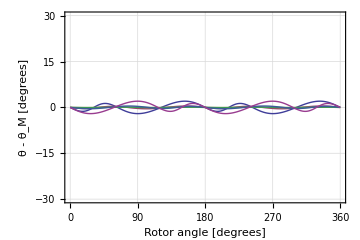

```mathematica
Module[{θ,θrad,θmeas,err,Corrected1,Corrected2,Corrected3,Corrected4,ωT,SimCorrect,Hzs},
splitstyle[styles__]:=Module[{st=Directive/@{styles}},{{Last[st=RotateLeft@st],#}}&];
θmeas[θ_]:=ArcTan[Cos[θ-ωT],Sin[θ]];
err[θ_] := θ-θmeas[θ];
Hzs={-10,-5,-2,2,5,10};
SimCorrect[θ_]:=θmeas[θ]+ωT/2(1- Cos[2 θmeas[θ]]);
Plot[
{Evaluate[Table[
ωT = Hz 2 π*0.0075;
θ = θrad π/180;
180/π( θ-If[SimCorrect[θ]<0,SimCorrect[θ]+2π,SimCorrect[θ]])
,{Hz,Hzs}]]}
,{θrad,0,360},AxesOrigin->{0,0},FrameLabel-> {"Rotor angle [degrees]","θ - θ_M [degrees]"},(*PlotLabel->"θ, θ_M1, and corrected θ_M",*)
Frame->{{True,True},{True,True}},PlotStyle->{Thick,splitstyle@@ColorData[1]/@{1,2,3,4,5,6}},
FrameTicks->{{0,90,180,270,360},Automatic,None,None},PlotRange->{{0,360},{-30,30}},
ImageSize->Medium,AspectRatio->2/3, FrameTicksStyle->Directive[22],BaseStyle->{FontSize->18},GridLines->Automatic,GridLinesStyle->Directive[Dotted,Lighter[Gray]]  (*less than 2 degrees error!*)
]]
```

```mathematica
Flatten[Table[{Thick,Directive[Thick,Dotted]},{n,4}]]
```

{Thickness[Large],Directive[Thickness[Large],Dashing[{0,Small}]],Thickness[Large],Directive[Thickness[Large],Dashing[{0,Small}]],Thickness[Large],Directive[Thickness[Large],Dashing[{0,Small}]],Thickness[Large],Directive[Thickness[Large],Dashing[{0,Small}]]}

```mathematica
^□■
```

```mathematica
Clear[ωT]
Manipulate[Module[{θ,θmeas,err,Corrected1,Corrected2,Corrected3,Corrected4,ωT,SimCorrect},
ωT = Hz 2 π/100;
θmeas[θ_]:=ArcTan[Cos[θ-ωT],Sin[θ]];
err[θ_] := θ-θmeas[θ];
SimCorrect[θ_]:=θmeas[θ]+ωT/2(1- Cos[2 θmeas[θ]]);

Plot[
{If[err[θD π/180]>π,err[θD π/180]-2π,err[θD π/180]]*180/π,(If[err[θD π/180]>π,err[θD π/180]-2π,err[θD π/180]]-ωT/2(1- Cos[2 θmeas[θD π/180]]))*180/π}

,{θD,0,360},AxesOrigin->{0,0},FrameLabel-> {"Rotor angle [Deg]","Measurements Error [Deg]"},PlotLabel->StringForm["Measurement error for θ_M1 and corrected θ_M at ``Hz",Hz],
Frame->{{True,False},{True,False}},
(*FrameTicks->{{0,Pi/2,Pi,3Pi/2,2Pi,3Pi},{0,Pi/2,Pi,3Pi/2,2Pi,3Pi}},*)
ImageSize->Medium,PlotStyle-> Thick, (*PlotStyle->{Automatic,Directive[Thick,Dashed],Directive[Thick,Dashing[{0.025,0.01}]]},*)
FrameTicksStyle->Directive[Automatic],BaseStyle->{FontSize->14},PlotRange->{{0,360},{-5,38}}
]],{{Hz,10,"Hz"},-15,15,Appearance->"Labeled"}]
```

```mathematica
Manipulate[Plot[{If[θ>π,θ-2π,θ],
-ⅈ Log[-(ⅈ ⅇ^((ⅈ ωT)/2) √(1+ⅇ^(2 ⅈ θmeas[θ])+ⅇ^(ⅈ ωT) (-1+ⅇ^(2 ⅈ θmeas[θ]))))/(√(-1+ⅇ^(2 ⅈ θmeas[θ])-2 Cos[θmeas[θ]] (Cos[θmeas[θ]+ωT]+ⅈ Sin[θmeas[θ]+ωT])))],-ⅈ Log[(ⅈ ⅇ^((ⅈ ωT)/2) √(1+ⅇ^(2 ⅈ θmeas[θ])+ⅇ^(ⅈ ωT) (-1+ⅇ^(2 ⅈ θmeas[θ]))))/(√(-1+ⅇ^(2 ⅈ θmeas[θ])-2 Cos[θmeas[θ]] (Cos[θmeas[θ]+ωT]+ⅈ Sin[θmeas[θ]+ωT])))]},{θ,0,2π},AxesOrigin->{0,0}, AxesLabel-> {"Actual θ angle","θ-θ_meas"},PlotLabel->"θ_meas and corrected θ_meas",PlotStyle->{Automatic,Directive[Thick,Dashed],Directive[Thick,Dashing[{0.005,0.01}]]}],{ωT,-5,25}]
```

## Ouajdis Version

```mathematica
ArcCos[θ]
```

```mathematica
Clear[ωT]
Manipulate[Module[{θ,θmeas,err,Corrected},
θmeas[θ_]:=ArcTan[Cos[θ-ωT],Sin[θ]];
err[θ_] := θ-θmeas[θ];
Corrected[θ_]:=θmeas[θ]+  ArcCos[Sin[θ]]- ArcCos[ Sin[θmeas[θ]]];
Plot[{θ,
If[θmeas[θ]<0,θmeas[θ]+2π,θmeas[θ]],
If[Corrected[θ]<0,Corrected[θ]+2π,Corrected[θ]]},{θ,0,2π},AxesOrigin->{0,0}, AxesLabel-> {"Actual θ angle","θ-θ_meas"},PlotLabel->"θ, θ_meas, and corrected θ_meas",PlotStyle->{Automatic,Directive[Thick,Dashed],Directive[Thick,Dashing[{0.005,0.01}]]}]],{{ωT,0.5,"ωT"},-π/2,π/2,Appearance->"Labeled"}]
```

```mathematica
Clear[ωT]
Manipulate[Module[{θ,θmeas,err,Corrected1,Corrected2,Corrected3,Corrected4,ωT,SimCorrect},
ωT = Hz 2 π/100;
θmeas[θ_]:=ArcTan[Cos[θ-ωT],Sin[θ]];
err[θ_] := θ-θmeas[θ];
Corrected1[θ_]:=θmeas[θ]+  ArcCos[Sin[θ]]- ArcCos[ Sin[θmeas[θ]]];
Corrected2[θ_]:=θmeas[θ]+  ArcSin[Sin[θ]]- ArcSin[ Sin[θmeas[θ]]];
Corrected3[θ_]:= ArcSin[Sin[θ]];
Corrected4[θ_]:= π-ArcSin[Sin[θ]];  
(*SimCorrect[θ_]:=θmeas[θ]+ωT/2(1- Cos[2 θmeas[θ]]);*)

Plot[{θ,
If[θmeas[θ]<0,θmeas[θ]+2π,θmeas[θ]],

(*If[Corrected1[θ]<0,Corrected1[θ]+2π,Corrected1[θ]],*)
(*If[Corrected2[θ]<0,Corrected2[θ]+2π,Corrected2[θ]],*)
If[Corrected3[θ]<0,Corrected3[θ]+2π,Corrected3[θ]],
If[Corrected4[θ]<0,Corrected4[θ]+2π,Corrected4[θ]]
(*If[SimCorrect[θ]<0,SimCorrect[θ]+2π,SimCorrect[θ]]*)

},{θ,0,2π},AxesOrigin->{0,0}, AxesLabel-> {"Actual θ angle","θ and θ estimates"},PlotLabel->"θ, θ_meas, and corrected θ_meas",Ticks->{{0,Pi/2,Pi,3Pi/2,2Pi,3Pi}},
Prolog->{
LightYellow,If[Hz>0,Rectangle[{π,0},{π 3/ 2,2π}],Rectangle[{π,0},{π 1/ 2,2π}]],
LightGreen,If[Hz>0,Rectangle[{0,0},{π /2,2π}],Rectangle[{3 π/2,0},{π  2,2π}]]
},
ImageSize->Large(*, PlotStyle->{Automatic,Directive[Thick,Dashed],Directive[Thick,Dashing[{0.025,0.01}]]}*)
]],{{Hz,3,"Hz"},-25,25,Appearance->"Labeled"}]
```

```mathematica
myWraptoTwopi[ϕ_]:=Module[{ϕ1,ϕ2},(ϕ1 = ϕ;While[ϕ1>π,ϕ1 = ϕ1-2π];ϕ2 = ϕ1; While[ϕ2<0,ϕ2 = ϕ2+2π]; Return[ϕ2])]
myWraptoTwopi[8]
myWraptoTwopi[-20]
```

8-2 π

-20+8 π

```mathematica
Clear[ωT]
myWraptoTwopi[ϕ_]:=Module[{ϕ1,ϕ2},(ϕ1 = ϕ;While[ϕ1>2π,ϕ1 = ϕ1-2π];ϕ2 = ϕ1;While[ϕ2<0,ϕ2 = ϕ2+2π]; Return[ϕ2])]
myWraptonegpiPospi[ϕ_]:=Module[{ϕ1,ϕ2},(ϕ1 = ϕ;While[ϕ1>π,ϕ1 = ϕ1-2π];ϕ2 = ϕ1;While[ϕ2<-π,ϕ2 = ϕ2+2π]; Return[ϕ2])]
Manipulate[Module[{θ,θmeas,ωT,SimCorrect,xmeas,zmeas,θa,θb,θpa,θpb,θinv,θda,θdb},
ωT = Hz 2 π/100;
xmeas= Cos[θ-ωT];
zmeas= Sin[θ];
θmeas=If[ArcTan[xmeas,zmeas]<0,ArcTan[xmeas,zmeas]+2π,ArcTan[xmeas,zmeas]];

(*there are two options for a given z measurement:*)
θa= myWraptoTwopi[ArcSin[zmeas]];
θb=myWraptoTwopi[ π-ArcSin[zmeas]];

(*calculate the angular differences from the two options from a given x measurement to the first z option:*)
θda=myWraptonegpiPospi[θa-(ArcCos[xmeas]+ωT )];
θdb=myWraptonegpiPospi[θa -(-ArcCos[xmeas]+ωT )];

θinv[θ_]:=  myWraptoTwopi[If[Abs[θda] < 0.001 ||Abs[θdb] < 0.001,  θa,θb]];

Plot[{θ,
(*θmeas,*)
θa,
(*θb,*)
θinv[θ]

},{θ,0,2π},AxesOrigin->{0,0}, AxesLabel-> {"Actual θ angle","θ and θ estimates"},PlotLabel->"θ, θ_meas, and corrected θ_meas",Ticks->{{0,Pi/2,Pi,3Pi/2,2Pi,3Pi}},
Prolog->{
LightYellow,If[Hz>0,Rectangle[{π,0},{π 3/ 2,2π}],Rectangle[{π,0},{π 1/ 2,2π}]],
LightGreen,If[Hz>0,Rectangle[{0,0},{π /2,2π}],Rectangle[{3 π/2,0},{π  2,2π}]]
},
ImageSize->Large, PlotStyle->{Automatic,Directive[Thick,Dashed],Directive[Thick,Dashing[{0.025,0.01}]]}
]],{{Hz,3,"Hz"},-25,25,Appearance->"Labeled"}]
```

### If the rotor is moving, what does the circle look like?

```mathematica
Manipulate[ParametricPlot[{{Cos[θ],Sin[θ]},{Cos[θ],Sin[θ+v/100]}},{θ,0,2π}],{{v,-20,"Angular Velocity [rad]"},-50,50,Appearance->"Labeled"}]
```

### Calculate True rotor position from 2 line scans ΔT seconds apart

```mathematica
MaxSpeed = 40;
CalcPosVel[θ_,dθ_]:=Module[{
x = Cos[θ- dθ/100],
z=Sin[θ],θest,vest},
θest =-ArcSin[z]-π;
vest =( θest+ArcCos[x])*100;

If[vest <0, θest =ArcSin[z];  vest =( θest+ArcCos[x])*100];
If[vest >MaxSpeed, θest =ArcSin[z];  vest =( θest-ArcCos[x])*100];
If[vest <0,θest = -ArcSin[z]-π; vest =( θest+2π-ArcCos[x])*100];

{θest,vest}]
te =Plot3D[
θest1 = CalcPosVel[θ,dθ]⟦1⟧;
Err = θ-θest1;
If[Err> π,Err-2π,If[Err<-π, Err+2π,Err]]
,
 {θ,-π,π},{dθ,0,MaxSpeed},PlotRange->{Automatic,Automatic,Automatic},AxesLabel->{"θ [rad]","dθ [rad/s]"},PlotLabel->"θ error",ImageSize->Medium];
de =Plot3D[
Vest = CalcPosVel[θ,dθ]⟦2⟧;
Errd =dθ-Vest,
 {θ,-π,π},{dθ,0,MaxSpeed},PlotRange->{Automatic,Automatic,Automatic},AxesLabel->{"θ [rad]","dθ [rad/s]"},PlotLabel->"dθ error",PlotRange->All];
GraphicsRow[{te,de}]
```

-Graphics-

```mathematica
{-1/100,1/100}
```

```mathematica
N[5*2*π/100*180/π]
```

18.

```mathematica
MaxSpeed = 50;
CalcPosVel[θ_,dθ_]:=Module[{
x = Cos[θ- dθ/100],
z=Sin[θ],θest,vest},
θest =-ArcSin[z]-π;
vest =( θest+ArcCos[x])*100;


If[vest <=-MaxSpeed, θest =ArcSin[z];  vest =( θest+ArcCos[x])*100];
If[vest >=MaxSpeed, θest =ArcSin[z];  vest =( θest-ArcCos[x])*100];
If[vest <=-MaxSpeed,θest = -ArcSin[z]-π; vest =( θest+2π-ArcCos[x])*100];

{θest,vest}]
te =Plot3D[
θest1 = CalcPosVel[θ,dθ]⟦1⟧;
Err = θ-θest1;
If[Err> π,Err-2π,If[Err<-π, Err+2π,Err]]
,
 {θ,0,2π},{dθ,-MaxSpeed,MaxSpeed},AxesLabel->{"θ [rad]","dθ [rad/s]"},PlotLabel->"θ error",ImageSize->Medium,LabelStyle->Directive[16]];
de =Plot3D[
Vest = CalcPosVel[θ,dθ]⟦2⟧;
Errd =dθ-Vest,
 {θ,0,2π},{dθ,-MaxSpeed,MaxSpeed},AxesLabel->{"θ [rad]","dθ [rad/s]"},PlotLabel->"dθ error",PlotRange->All,ImageSize->Medium,LabelStyle->Directive[16]];
GraphicsRow[{te,de},ImageSize->Medium]
```

-Graphics-

```mathematica
MaxSpeed = 100;
te =Plot3D[
x = Cos[θ- dθ/100]
,
 {θ,0,2π},{dθ,-MaxSpeed,MaxSpeed},AxesLabel->{"θ","dθ [rad/s]"},PlotLabel->"X measurement",ImageSize->Medium,LabelStyle->Directive[16]];
de =Plot3D[
z=Sin[θ],
 {θ,0,2π},{dθ,-MaxSpeed,MaxSpeed},AxesLabel->{"θ","dθ [rad/s]"},PlotLabel->"Z measurement",PlotRange->All,ImageSize->Medium,LabelStyle->Directive[16]];
GraphicsRow[{te,de},ImageSize->Medium]
```

-Graphics-

```mathematica
Switching charts based on my current velocity estimte.  (operating points)
```

### Could we detect the velocity of a moving rotor? Yes -- if the velocity is positive, then we measure outside the unit circle in quad 1 and 3, inside in quadrants 2 and 4. The oposite is true if our velocity is negative. We could throw information like this into the Kalman filter. TODO: plot radius measurement as a function of velocity and θ_meas plot error as a functin of velocity and θ_meas Other ways to improve: pick measurement inputs that cause desired actuation. Is two measurements sufficient to learn position & velocity?

```mathematica
Manipulate[
dt = 7.5/1000; (*time between x and z is 7.5ms *)
rotorLengthmm = 16; (*rotor length, mm*)
θZ = θstart+dt*angVel 2 π;
θMeas = ArcTan[Cos[θstart],Sin[θZ]];
Graphics[{
Gray,Disk[{0,0},rotorLengthmm,{θstart,θZ }],
Green,Thickness[0.03],Line[{{0,0},rotorLengthmm{Cos[θstart],Sin[θstart]}}],

Red,Thickness[0.02],Line[{{0,0},rotorLengthmm{Cos[θZ],Sin[θZ]}}],

Purple,Thickness[0.01], Line[{{0,0},rotorLengthmm{Cos[θMeas],Sin[θMeas]}}],

Green,Thickness[0.005],Line[rotorLengthmm{{Cos[θstart],-1},{Cos[θstart],1}}],
Red,Thickness[0.005],Line[rotorLengthmm{{-1,Sin[θZ]},{1,Sin[θZ]}}],
Blue,Thickness[0.005], (*possible positions of scanner*)
Circle[{0,0},rotorLengthmm]
},ImageSize->500],
{θstart,0,2 π,Appearance->"Labeled"},{{angVel,1, "Angular Velocity [Hz]"},-10,10,Appearance->"Labeled"}  (*Hz*)]
```

```mathematica
25/1000*5
```

1/8

### Data from Single Rotor test Rotor in head coil, on 16 mm rotor, spinning parallel with y (vertical) axis. Open loop at 1 Hz at first, then off for ‘closed-loop’ section, I manually moved it from pointing between zx to point between x-z

```mathematica
SetDirectory[NotebookDirectory[]];
str =Import["positions.txt","Text"];
(*split out the {...} sections*)
points=ToExpression/@StringCases[ str,"{"~~Except["}"]..~~"}"];
(*only save groups of 3 numbers*)
validData=Select[points,3==Length[DeleteCases[#,Null]]&];
```

```mathematica
Length[validData]
```

71

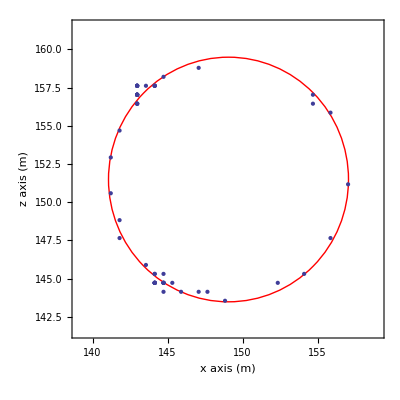

```mathematica
cx = 149.026;
cy =151.519;
rad = 8;
ListPlot[Table[{validData[[i,2]],
validData[[i,3]]},{i,1,Length[validData]}],AspectRatio->Automatic,Mesh-> All,Frame->True,Joined->False,FrameLabel->{"x axis (m)","z axis (m)"},
MeshStyle->Directive[PointSize[Large],Red],AspectRatio->Automatic,FrameTicksStyle->Directive[16],LabelStyle->Directive[18],PlotRange->{{-10,10}+cx,{-10,10}+cy},Prolog->{Red,Circle[{cx,cy},rad]}]
```

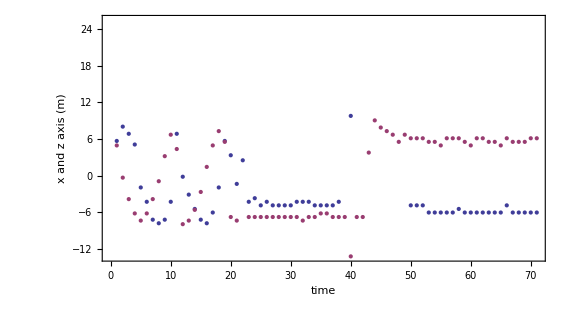

```mathematica
ListPlot[{validData[[;;,2]]-cx,
validData[[;;,3]]-cy},AspectRatio->Automatic,Mesh-> All,Frame->True,Joined->False,FrameLabel->{"time","x and z axis (m)"},
MeshStyle->Directive[PointSize[Large],Red],FrameTicksStyle->Directive[16],LabelStyle->Directive[18]]
```

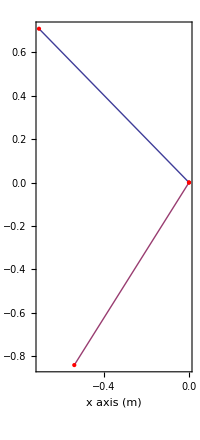

```mathematica
T1= 2.35285   ;
T2 = -2.14;
ListPlot[{ {{0,0},{Cos[T1],Sin[T1]}},{{0,0},{Cos[T2],Sin[T2]}}},

Frame->True,Joined->True,Mesh->All,AxesOrigin->{0,0},FrameLabel->{"x axis (m)","z axis (m)"},MeshStyle->Directive[PointSize[Large],Red],AspectRatio->Automatic,FrameTicksStyle->Directive[16],LabelStyle->Directive[18]]
```

```mathematica
ParametricPlot3D[Evaluate[Table[{(2+Cos[8u+i])Cos[u],(2+Cos[8u+i])Sin[u],Sin[8u+i]},{i,{0,Pi}}]],{u,0,2Pi}, AxesOrigin->{0,0,0},Boxed->False]
```

-Graphics3D-

### Plot the different open - loop control axis

```mathematica
RotationMatrix[{{0,0,1},{0,0,-1}}]
```

RotationMatrix::spln: Vectors {0, 0, 1} and {0, 0, -1} do not define a plane.

{{1,0,0},{0,-1,0},{0,0,-1}}

```mathematica
{{0,0,1},{0,1,0},{-1,0,0}}.{rad Cos[u],rad Sin[u],0.8}
```

{0.8,0.+0.2 Sin[u],0.-0.2 Cos[u]}

```mathematica
rad = 0.2;
vecs =Flatten[Table[Evaluate[vNorm=√(Vx^2+Vy^2+Vz^2);If[vNorm==0,{0,0,0},{Vx,Vy,Vz}/vNorm]],{Vx,{-1,0,1}},{Vy,{-1,0,1}},{Vz,{-1,0,1}}],2];
cols = {Red,Blue,Red,Blue,Green,Blue,Red,Blue,Red,
Blue,Green,Blue,Green,Blue,Green,Blue,Green,Blue,
Red,Blue,Red,Blue,Green,Blue,Red,Blue,Red};
circs = ParametricPlot3D[Evaluate[Flatten[Table[v ={Vx,Vy,Vz}; If[v == {0,0,0},v = {1,0,0}];RotationMatrix[{{0,0,1},v}].{rad Cos[u],rad Sin[u],0.8},{Vx,{-1,0,1}},{Vy,{-1,0,1}},{Vz,{-1,0,1}}],2]],{u,0,15/8Pi}, AxesOrigin->{0,0,0},Boxed->False,AspectRatio->Automatic,PlotStyle->Table[Directive[{Thick,col}],{col,cols}]
]
```

RotationMatrix::spln: Vectors {0, 0, 1} and {0, 0, -1} do not define a plane.

-Graphics3D-

```mathematica
Graphics3D[{Thick,Flatten[Table[v ={Vx,Vy,Vz}; If[v == {0,0,0},v = {1,0,0}];Arrow[BSplineCurve[Table[RotationMatrix[{{0,0,1},v}].{rad Cos[u],rad Sin[u],0.8},{u,0,15/8Pi,Pi/20}]]],{Vx,{-1,0,1}},{Vy,{-1,0,1}},{Vz,{-1,0,1}}],2]}
]
```

RotationMatrix::spln: Vectors {0, 0, 1} and {0, 0, -1} do not define a plane.

General::stop: Further output of RotationMatrix :: spln will be suppressed during this calculation.

-Graphics3D-

```mathematica
vecs
```

{{-1/(√3),-1/(√3),-1/(√3)},{-1/(√2),-1/(√2),0},{-1/(√3),-1/(√3),1/(√3)},{-1/(√2),0,-1/(√2)},{-1,0,0},{-1/(√2),0,1/(√2)},{-1/(√3),1/(√3),-1/(√3)},{-1/(√2),1/(√2),0},{-1/(√3),1/(√3),1/(√3)},{0,-1/(√2),-1/(√2)},{0,-1,0},{0,-1/(√2),1/(√2)},{0,0,-1},{0,0,0},{0,0,1},{0,1/(√2),-1/(√2)},{0,1,0},{0,1/(√2),1/(√2)},{1/(√3),-1/(√3),-1/(√3)},{1/(√2),-1/(√2),0},{1/(√3),-1/(√3),1/(√3)},{1/(√2),0,-1/(√2)},{1,0,0},{1/(√2),0,1/(√2)},{1/(√3),1/(√3),-1/(√3)},{1/(√2),1/(√2),0},{1/(√3),1/(√3),1/(√3)}}

```mathematica
Graphics3D[{ 
Flatten[v =vecsS⟦1⟧; If[v == {0,0,0},v = {1,0,0}];{cols⟦1⟧,Thick,Arrow[BSplineCurve[Table[RotationMatrix[{{0,0,1},v}].{rad Cos[u],rad Sin[u],0.8},{u,0,15/8Pi,Pi/5}]]]},2]
}]
```

```mathematica
Graphics3D[{ 
Flatten[v =vecsS⟦1⟧; If[v == {0,0,0},v = {1,0,0}];{cols⟦1⟧,Thick,Arrow[BSplineCurve[Table[RotationMatrix[{{0,0,1},v}].{rad Cos[u],rad Sin[u],0.8},{u,0,15/8Pi,Pi/5}]]]},2]
}]
Graphics3D[{ 
v =vecsS⟦1⟧; If[v == {0,0,0},v = {1,0,0}];{cols⟦1⟧,Thick,Arrow[BSplineCurve[Table[RotationMatrix[{{0,0,1},v}].{rad Cos[u],rad Sin[u],0.8}.proj,{proj, {{1,0,0},{0,1,0},{0,0,1}}},{u,0,15/8Pi,Pi/5}]]]},
}]
```

-Graphics3D-

-Graphics3D-

```mathematica
(*a xx Mb file!*)
vecs =Flatten[Table[Evaluate[vNorm=√(Vx^2+Vy^2+Vz^2);If[vNorm==0,{0,0,0},{Vx,Vy,Vz}/vNorm]],{Vx,{-1,0,1}},{Vy,{-1,0,1}},{Vz,{-1,0,1}}],2];
vecsS =Flatten[Table[{Vx,Vy,Vz},{Vx,{-1,0,1}},{Vy,{-1,0,1}},{Vz,{-1,0,1}}],2];
cols = {Red,Blue,Red,Blue,Green,Blue,Red,Blue,Red,
Blue,Green,Blue,Green,Green,Green,Blue,Green,Blue,
Red,Blue,Red,Blue,Green,Blue,Red,Blue,Red};


Graphics3D[{Table[Arrow[{{0,0,0},v}],{v,{{1,0,0},{-1,0,0},{0,1,0},{0,-1,0},{0,0,1},{0,0,-1}}}],
Flatten[Table[v =vecsS⟦i⟧; If[v == {0,0,0},v = {1,0,0}];{cols⟦i⟧,Thick,Arrow[BSplineCurve[Table[RotationMatrix[{{0,0,1},v}].{rad Cos[u],rad Sin[u],0.8},{u,0,15/8Pi,Pi/5}]]]},{i,1,Length[vecsS]}],2]

(*Arrowheads[0.05],Table[{cols⟦i⟧,Arrow[Tube[{{0,0,0},0.5vecs⟦i⟧},0.015]]},{i,1,Length[vecs]}]*)

},Boxed->False
]
```

RotationMatrix::spln: Vectors {0, 0, 1} and {0, 0, -1} do not define a plane.

General::stop: Further output of RotationMatrix :: spln will be suppressed during this calculation.

-Graphics3D-

```mathematica
(*a 320 Mb file!*)
vecs =Flatten[Table[Evaluate[vNorm=√(Vx^2+Vy^2+Vz^2);If[vNorm==0,{0,0,0},{Vx,Vy,Vz}/vNorm]],{Vx,{-1,0,1}},{Vy,{-1,0,1}},{Vz,{-1,0,1}}],2];
vecsS =Flatten[Table[{Vx,Vy,Vz},{Vx,{-1,0,1}},{Vy,{-1,0,1}},{Vz,{-1,0,1}}],2];
cols = {Red,Blue,Red,Blue,Green,Blue,Red,Blue,Red,
Blue,Green,Blue,Green,Blue,Green,Blue,Green,Blue,
Red,Blue,Red,Blue,Green,Blue,Red,Blue,Red};


Graphics3D[{Table[Arrow[{{0,0,0},v}],{v,{{1,0,0},{-1,0,0},{0,1,0},{0,-1,0},{0,0,1},{0,0,-1}}}],
Flatten[Table[v =vecsS⟦i⟧; If[v == {0,0,0},v = {1,0,0}];{cols⟦i⟧,Arrow[Tube[Table[RotationMatrix[{{0,0,1},v}].{rad Cos[u],rad Sin[u],0.8},{u,0,15/8Pi,Pi/20}],0.015]]},{i,1,Length[vecsS]}],2],

(*Arrowheads[0.05],Table[{cols⟦i⟧,Arrow[Tube[{{0,0,0},0.5vecs⟦i⟧},0.015]]},{i,1,Length[vecs]}]*)

},Boxed->False
]
```

RotationMatrix::spln: Vectors {0, 0, 1} and {0, 0, -1} do not define a plane.

General::stop: Further output of RotationMatrix :: spln will be suppressed during this calculation.

-Graphics3D-

```mathematica
vecs =Flatten[Table[Evaluate[vNorm=√(Vx^2+Vy^2+Vz^2);If[vNorm==0,{0,0,0},{Vx,Vy,Vz}/vNorm]],{Vx,{-1,0,1}},{Vy,{-1,0,1}},{Vz,{-1,0,1}}],2];
vecsS =Flatten[Table[{Vx,Vy,Vz},{Vx,{-1,0,1}},{Vy,{-1,0,1}},{Vz,{-1,0,1}}],2];
cols = {Red,Blue,Red,Blue,Green,Blue,Red,Blue,Red,
Blue,Green,Blue,Green,Blue,Green,Blue,Green,Blue,
Red,Blue,Red,Blue,Green,Blue,Red,Blue,Red};
VecArr =Graphics3D[{Arrowheads[0.05],Table[{cols⟦i⟧,Arrow[Tube[{{0,0,0},0.75vecs⟦i⟧},0.015]]},{i,1,Length[vecs]}]}]
```

-Graphics3D-

```mathematica
vecs =Flatten[Table[Evaluate[vNorm=√(Vx^2+Vy^2+Vz^2);If[vNorm==0,{0,0,0},{Vx,Vy,Vz}/vNorm]],{Vx,{-1,0,1}},{Vy,{-1,0,1}},{Vz,{-1,0,1}}],2];
cols = {Red,Blue,Red,Blue,Green,Blue,Red,Blue,Red,
Blue,Green,Blue,Green,Blue,Green,Blue,Green,Blue,
Red,Blue,Red,Blue,Green,Blue,Red,Blue,Red};
VecArr =Graphics3D[{Arrowheads[0.05],Table[{cols⟦i⟧,Arrow[Tube[{{0,0,0},0.75vecs⟦i⟧},0.015]]},{i,1,Length[vecs]}]}]
```

-Graphics3D-

```mathematica
Show[{circs,VecArr}]
```

-Graphics3D-

```mathematica
vecs =Table[{Vx,Vy,Vz},{Vx,{-1,0,1}},{Vy,{-1,0,1}},{Vz,{-1,0,1}}]
```

{{{{-1,-1,-1},{-1,-1,0},{-1,-1,1}},{{-1,0,-1},{-1,0,0},{-1,0,1}},{{-1,1,-1},{-1,1,0},{-1,1,1}}},{{{0,-1,-1},{0,-1,0},{0,-1,1}},{{0,0,-1},{0,0,0},{0,0,1}},{{0,1,-1},{0,1,0},{0,1,1}}},{{{1,-1,-1},{1,-1,0},{1,-1,1}},{{1,0,-1},{1,0,0},{1,0,1}},{{1,1,-1},{1,1,0},{1,1,1}}}}

```mathematica
Table[Evaluate[vNorm=√(Vx^2+Vy^2+Vz^2);If[vNorm==0,{0,0,0},{Vx,Vy,Vz}/vNorm]],{Vx,{-1,0,1}},{Vy,{-1,0,1}},{Vz,{-1,0,1}}]
```

{{{{-1/(√3),-1/(√3),-1/(√3)},{-1/(√2),-1/(√2),0},{-1/(√3),-1/(√3),1/(√3)}},{{-1/(√2),0,-1/(√2)},{-1,0,0},{-1/(√2),0,1/(√2)}},{{-1/(√3),1/(√3),-1/(√3)},{-1/(√2),1/(√2),0},{-1/(√3),1/(√3),1/(√3)}}},{{{0,-1/(√2),-1/(√2)},{0,-1,0},{0,-1/(√2),1/(√2)}},{{0,0,-1},{0,0,0},{0,0,1}},{{0,1/(√2),-1/(√2)},{0,1,0},{0,1/(√2),1/(√2)}}},{{{1/(√3),-1/(√3),-1/(√3)},{1/(√2),-1/(√2),0},{1/(√3),-1/(√3),1/(√3)}},{{1/(√2),0,-1/(√2)},{1,0,0},{1/(√2),0,1/(√2)}},{{1/(√3),1/(√3),-1/(√3)},{1/(√2),1/(√2),0},{1/(√3),1/(√3),1/(√3)}}}}

```mathematica
MatrixForm[{Vx,Vy,Vz}]
```

(Vx
Vy
Vz)

```mathematica
{Vx,Vy,Vz}/√(Vx^2+Vy^2+Vz^2)
```

{Vx/(√(Vx^2+Vy^2+Vz^2)),Vy/(√(Vx^2+Vy^2+Vz^2)),Vz/(√(Vx^2+Vy^2+Vz^2))}

```mathematica
PLot θ and dθ
```

Plot::exclul: {Im[θ] - 0, Im[Sin[ArcTan[Cos["\[Omega]T" + Times[« 2 »]], Sin[θ]]]] - 0} must be a list of equalities or real-valued functions.

$Aborted